# Estrategias de trading basadas en medias móviles

## Inicialización

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{NotebookDirectory[],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

### Información de los paquetes cargados

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

## Cargar base de datos

```mathematica
path = FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}];
database = Import[path];
database[[All,"Name"]] = {"DJIA","DAX","IPC","Nikkei 225"};
```

## Cálculo de entropía

```mathematica
market = First[database];
```

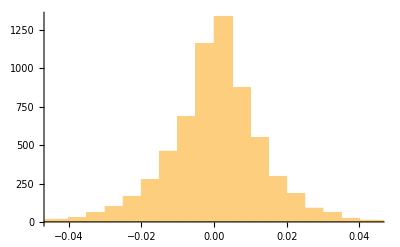

```mathematica
Histogram[market["Returns"]]
```

```mathematica
quantiles = Quantile[market["Returns"],{1/4,1/2,3/4}]
```

{-0.00650255,0.000879896,0.00763187}

```mathematica
intervals = Partition[Join[{-∞},quantiles,{∞}],2,1]
```

{{-∞,-0.00650255},{-0.00650255,0.000879896},{0.000879896,0.00763187},{0.00763187,∞}}

```mathematica
discreteStates = Range[Length[intervals]]
```

{1,2,3,4}

```mathematica
rules = MapThread[x_/;IntervalMemberQ[Interval[#1],x]->#2&,{intervals,discreteStates}]
```

{x_/;IntervalMemberQ[Interval[{-∞,-0.00650255}],x]→1,x_/;IntervalMemberQ[Interval[{-0.00650255,0.000879896}],x]→2,x_/;IntervalMemberQ[Interval[{0.000879896,0.00763187}],x]→3,x_/;IntervalMemberQ[Interval[{0.00763187,∞}],x]→4}

```mathematica
discretization = market["Returns"]/. rules;
```

```mathematica
Entropy[discretization]
```

(-4848 Log[1616]-1617 Log[1617])/6465+Log[6465]

```mathematica
N[Entropy[discretization]]
```

1.38629

El procedimiento en general se puede encapsular en una función:

```mathematica
DiscretizeByQuartiles[returns_]:=Block[{quantiles,intervals,discreteStates,rules},
quantiles = Quantile[returns,{1/4,1/2,3/4}];
intervals = Partition[Join[{-∞},quantiles,{∞}],2,1];
discreteStates = Range[Length[intervals]];
rules = MapThread[x_/;IntervalMemberQ[Interval[#1],x]->#2&,{intervals,discreteStates}];

returns/. rules
];
```

Con esta función el procedimiento de discretización se puede resumir:

```mathematica
Take[DiscretizeByQuartiles[market["Returns"]],20]
```

{3,3,3,2,3,1,1,2,3,1,4,1,3,1,1,3,4,2,3,2}

## Evolución temporal de la entropía de un mercado

```mathematica
dowJonesDiscreto = market["Returns"]/.rules;
```

```mathematica
discretoConFechas =Transpose[{Drop[market["Dates"],-1],dowJonesDiscreto}];
parts = Partition[discretoConFechas,50,1];
```

```mathematica
resultado  = Map[
{
Last[#[[All,1]]],
N[Entropy[#[[All,2]]]]
}&,
parts
];
```

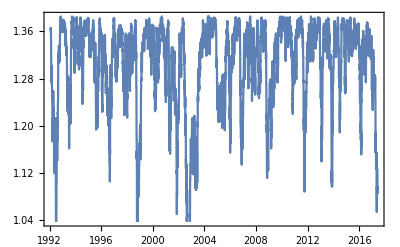

```mathematica
DateListPlot[resultado]
```

## Comparación con caminante aleatorio

Dado de que la distribución de los retornos se aproxima a una gaussiana,

```mathematica
Histogram[market["Returns"]]
```

-Graphics-

se compararán los resultados del cálculo de entropía para un caminante aleatorio, es decir, retornos generados a partir de una distribución gaussiana.

```mathematica
Length[market["Returns"]]
```

6465

```mathematica
fakeReturns = RandomVariate[NormalDistribution[],6465];
```

```mathematica
discretized = DiscretizeByQuartiles[fakeReturns];
```

```mathematica
parts = Partition[discretized,50,1];
```

```mathematica
resultadoGaussiano = Map[Entropy,parts];
```

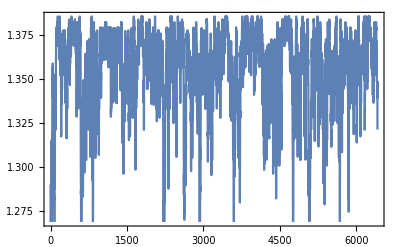

```mathematica
ListLinePlot[resultadoGaussiano,Frame->True]
```

Y la comparación:

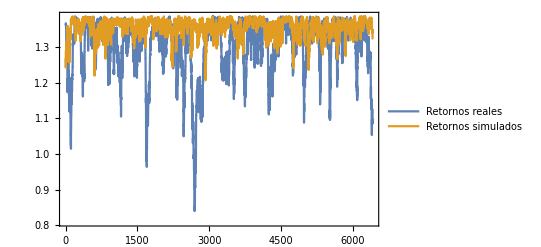

```mathematica
ListLinePlot[{resultado[[All,2]],resultadoGaussiano},Frame->True,PlotLegends->{"Retornos reales","Retornos simulados"},PlotRange->All]
```